```mathematica
Data = {{2,0.49906568404477153},
{3,0.41669345554793435},
{4,0.37570216952691693},
{5,0.35055786770819547},
{6,0.3333207268009721},
{7,0.3213405098883921},
{8,0.3121795720311473}
}
```

{{2,0.499066},{3,0.416693},{4,0.375702},{5,0.350558},{6,0.333321},{7,0.321341},{8,0.31218}}

```mathematica
Data[[1,1]]
```

2

```mathematica
NewData = {};

For[i =1, i <= Length[Data], i++, 
temp = Data[[i,1]];
prob = Data[[i,2]];
AppendTo[NewData, { 1/temp, 1 + prob *Log[prob] /Log[2]+ (1- prob)* Log[1-prob]/Log[2]}]
]
```

```mathematica
NewData
```

{{1/2,2.51879×10^-6},{1/3,0.0201182},{1/4,0.04505},{1/5,0.0654347},{1/6,0.0817168},{1/7,0.0941667},{1/8,0.104327}}

```mathematica
Plot[NewData,{x,y}]
```

Plot::pllim: Range specification {x,y} is not of the form {x, xmin, xmax}.

Plot[NewData,{x,y}]

```mathematica
ListPlot[NewData, {x,0,0.5} , {y,0, 1}]
```

ListPlot::nonopt: Options expected (instead of {y,0,1}) beyond position 1 in ListPlot[{{1/2,2.51879×10^-6},{1/3,0.0201182},{1/4,0.04505},{1/5,0.0654347},{1/6,0.0817168},{1/7,0.0941667},{1/8,0.104327}},{x,0,0.5},{y,0,1}]. An option must be a rule or a list of rules.

ListPlot[{{1/2,2.51879×10^-6},{1/3,0.0201182},{1/4,0.04505},{1/5,0.0654347},{1/6,0.0817168},{1/7,0.0941667},{1/8,0.104327}},{x,0,0.5},{y,0,1}]

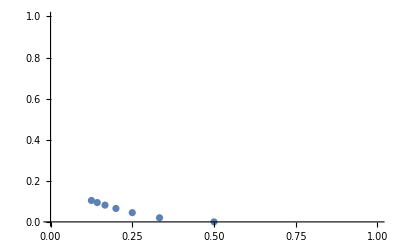

```mathematica
ListPlot[NewData,PlotRange->{{0,1},{0,1}}]
```